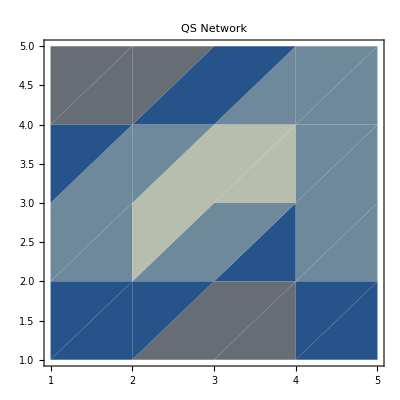

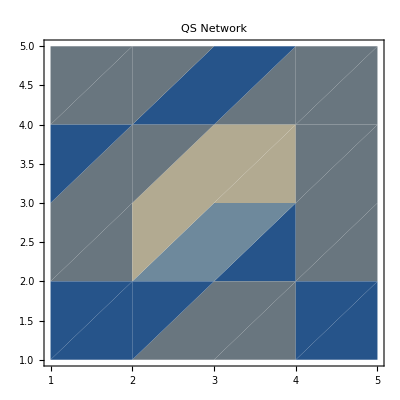

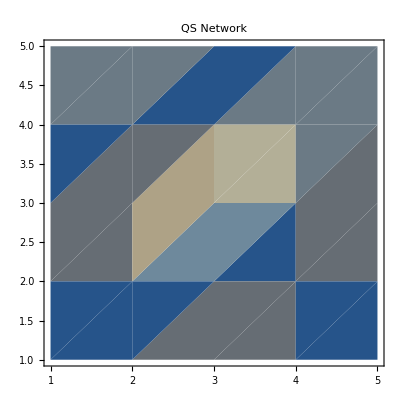

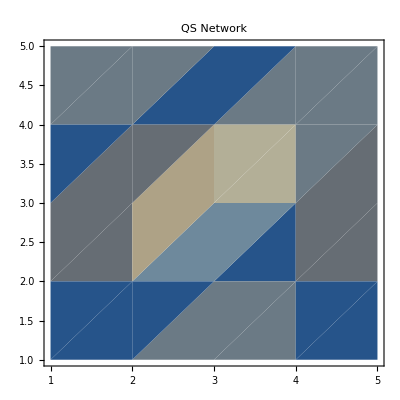

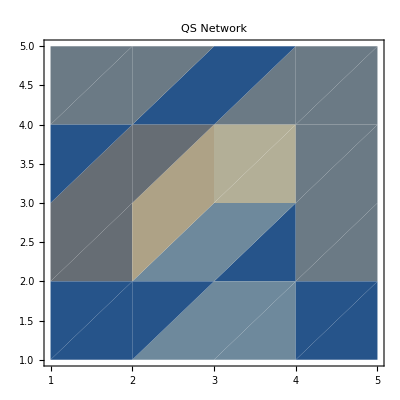

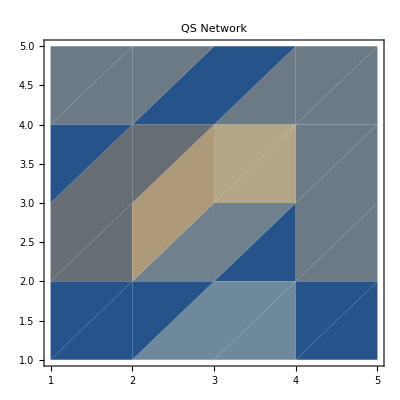

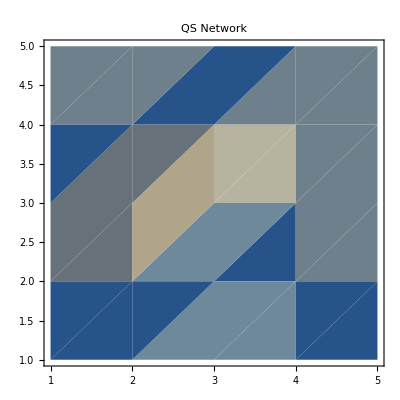

-Graphics-

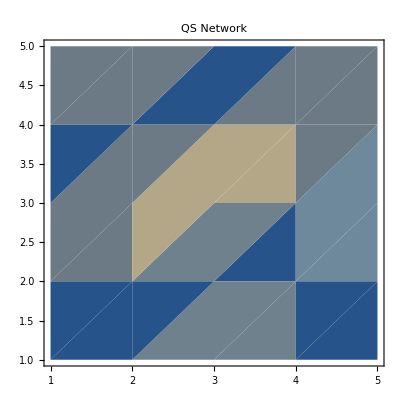

-Graphics-

D:\Neu_cell-cell\Cell-cell communication {QS based}\QS basics - testing neighbors 02-22-20

{10,5,5}

Signal-lccore-control-5x5.csv

```mathematica
areaSize=5;
cellDensity=0.2;
observationTime=10;
timeforSignaling=1;

cellDistribution[]:=HalfNormalDistribution[0.5];

(*Auxiliary signalling functions*)
neigh={};
For[k=1,k≤15,k++,
neighborhood=Table[Max[0,k-Abs[x]-Abs[y]],{x,-5,5},{y,-5,5}];
neigh=Append[neigh,neighborhood]];

aiDomain={1,2,3,4,5,6,7,8,9,10};

aiConcentration[level_]:=Switch[level,1,neigh[[3]],2,neigh[[5]],3,neigh[[7]],4,neigh[[9]],5,neigh[[8]],6,neigh[[7]],7,neigh[[6]],8,neigh[[5]],9,neigh[[4]],10,neigh[[3]]];

aiCell[level_]:=Switch[level,1,1,2,3,3,5,4,7,5,6,6,5,7,4,8,3,9,2,10,1];

aiDistance[level_]:=1+aiCell[level];

aiUpdate[levels_,lccore_]:=(levelsNew=levels;
cellPos1=Position[levels[[First[aiDomain]]],1];
conc1=Extract[lccore,cellPos1];
For[s=1,s≤Length[conc1],s++,If[conc1[[s]]>First[aiDomain]+3,levelsNew[[First[aiDomain]+1]]=ReplacePart[levelsNew[[First[aiDomain]+1]],1,cellPos1[[s]]];levelsNew[[First[aiDomain]]]=ReplacePart[levelsNew[[First[aiDomain]]],0,cellPos1[[s]]]];
];
Clear[cellPos1,conc1];
cellPos1=Position[levels[[Last[aiDomain]]],1];
conc1=Extract[lccore,cellPos1];
For[s=1,s≤Length[conc1],s++,If[conc1[[s]]<Last[aiDomain]+3,levelsNew[[Last[aiDomain]-1]]=ReplacePart[levelsNew[[Last[aiDomain]-1]],1,cellPos1[[s]]];
levelsNew[[Last[aiDomain]]]=ReplacePart[levelsNew[[Last[aiDomain]]],0,cellPos1[[s]]]];
];
Clear[cellPos1,conc1];
For[r=First[aiDomain]+1,r<Last[aiDomain],r++,
cellPos1=Position[levels[[r]],1];
conc1=Extract[lccore,cellPos1];
For[s=1,s≤Length[conc1],s++,
If[conc1[[s]]<r+3,levelsNew[[r-1]]=ReplacePart[levelsNew[[r-1]],1,cellPos1[[s]]];levelsNew[[r]]=ReplacePart[levelsNew[[r]],0,cellPos1[[s]]],If[conc1[[s]]>r+3,levelsNew[[r+1]]=ReplacePart[levelsNew[[r+1]],1,cellPos1[[s]]];levelsNew[[r]]=ReplacePart[levelsNew[[r]],0,cellPos1[[s]]]];];];
];
Clear[cellPos1,conc1];
levelsNew
);

(*Initializing all necessary data structures*)
levels=Table[0,{Last[aiDomain]-First[aiDomain]+1},{areaSize},{areaSize}];
levelsDynamic=levels;
levelsDynamicNew=levels;
levelsStatic=levels;
graph=Range[observationTime];
productionList=Range[observationTime];
cells=Table[If[Random[]<cellDensity,1,0],{i,areaSize},{j,areaSize}];
cells={{0,0,1,0,0},{0,0,0,0,0},{0,1,1,0,1},{0,0,0,1,0},{0,1,0,0,0}};
(*cell position specified*)
levels=ReplacePart[levels,cells,1];
lc=ListCorrelate[aiConcentration[1],cells,{-1,1},0];
lccore=lc[[6;;areaSize+5,6;;areaSize+5]];
levels=aiUpdate[levels,lccore];

nCells=Count[cells,1,2];
cellPos=Position[cells,1];
EdgeMatrix=Table[0,{nCells},{nCells}];

(*Main QS cycle*)
For[clock=1,clock≤observationTime,clock++,
(*update level and concentration table*)
If[Mod[clock,timeforSignaling]==0,
lc=Plus@@Function[{i},ListCorrelate[aiConcentration[i],levels[[i]],{-1,1},0]]/@aiDomain;
lccore=lc[[6;;areaSize+5,6;;areaSize+5]];
signalingCells=cells; 
For[k=1,k≤nCells,k++,
(*To avoid artificial cyclic activation-inhibition dependencies, only a small fraction of cells is signalling at once*)
If[Random[]<.8,signalingCells=ReplacePart[signalingCells,0,cellPos[[k]]]];
];
For[k=First[aiDomain],k≤Last[aiDomain],k++,
levelsStatic[[k]]=levels[[k]]-signalingCells;
mins=Position[levelsStatic[[k]],-1];
For[v=1,v≤Length[mins],v++,levelsStatic[[k]]=ReplacePart[levelsStatic[[k]],0,mins[[v]]]];
];
levelsDynamic=levels-levelsStatic;
levelsDynamicNew=aiUpdate[levelsDynamic,lccore];
levels=levelsDynamicNew+levelsStatic;
];
graph[[clock]]=Plus@@Function[{i},aiDistance[i]*levels[[i]]]/@aiDomain;
Print[ListDensityPlot[graph[[clock]],PlotLabel->"QS Network"]];
productionList[[clock]]=N[Total[graph[[clock]],2]/nCells](*average ai production per cell*)
]; (*end main QS cycle*)

(*Pathway Analysis*)
EdgeMatrix=Table[0,{nCells},{nCells}];
highlyConnectedCells=Table[0,{nCells}];
nHighlyConnected=0;
For[k=1,k≤nCells,k++,
maxDist=Last[graph][[cellPos[[k,1]],cellPos[[k,2]]]];
For[v=1,v≤nCells,v++,
If[k==v,Continue[]];
dist=Abs[cellPos[[k,1]]-cellPos[[v,1]]]+Abs[cellPos[[k,2]]-cellPos[[v,2]]];
If[dist≤maxDist,EdgeMatrix[[k,v]]++];];
];
totalEdgeMatrix=Total[EdgeMatrix,{2}];
For[k=1,k≤nCells,k++,
If[totalEdgeMatrix[[k]]>5,nHighlyConnected++;highlyConnectedCells[[k]]=1];
];

SetDirectory["D:\\Neu_cell-cell\\Cell-cell communication {QS based}\\QS basics - testing neighbors 02-22-20"]
Dimensions[graph]
graph1=ArrayReshape[graph,{10,25}];
Export["Signal-lccore-control-5x5.csv",graph1,"CSV"]
```

```mathematica
cells
```

{{0,0,1,0,0},{0,0,0,0,0},{0,1,1,0,1},{0,0,0,1,0},{0,1,0,0,0}}